```mathematica
.14
```

### Example Mathematica notebook of algorithm referred to in “Waterfront on the Martian Planitia: Algorithmic emergent catchments on disordered terrain” Handmer 2016, arXiv:1606.05224

#### casey<dot>handmer@gmail.com

#### Raw data is obtained from the MOLA dataset

```mathematica
raw=-Graphics-;
```

```mathematica
dat=ImageData[raw];
```

#### Two separate vectorized RHS computations, one for latitudinal and one for longitudinal calculations.

```mathematica
elementarea=Table[Sin[π (i-1.)/(Length[dat]-1.)],{i,1,Length[dat],1}];
elementarea[[1]]=elementarea[[2]];
elementarea[[-1]]=elementarea[[-2]];
eamat=Transpose[Table[elementarea,{Length[dat[[1]]]}]];

NewDepthDelta1Dperiodic[alts_,depths_,stepsize_]:=Catch[
adghost=Transpose[Join[Transpose[#[[All,-2;;-1]]],Transpose[#],Transpose[#[[All,1;;2]]]]]&[alts+depths];
dghost=Transpose[Join[Transpose[#[[All,-2;;-1]]],Transpose[#],Transpose[#[[All,1;;2]]]]]&[depths];
righttransport=(#[[All,1;;-2]]-#[[All,2;;-1]])&[adghost];
rtp=#(0.5+0.5Sign[#])&[righttransport];
rtn=#(0.5-0.5Sign[#])&[righttransport];
losses=stepsize Transpose[{-rtn[[All,1;;-2]],rtp[[All,2;;-1]]},{3,1,2}];
adjustedlosses=losses((0.5+0.5#)+dghost[[All,2;;-2]](0.5-0.5#)/((0.5+0.5#)+Total[Transpose[losses,{2,3,1}]]))&[Sign[dghost[[All,2;;-2]]-Total[Transpose[losses,{2,3,1}]]]];
.14ma
Throw[eamat(adjustedlosses[[All,1;;-3,2]]+adjustedlosses[[All,3;;-1,1]]-Total[Transpose[adjustedlosses[[All,2;;-2]],{2,3,1}]])]];
```

```mathematica
elementarea=Table[Sin[π (i-1.)/(Length[dat]-1.)],{i,1,Length[dat],1}];
elementarea[[1]]=elementarea[[2]];
elementarea[[-1]]=elementarea[[-2]];
earatio=elementarea[[1;;-2]]/elementarea[[2;;-1]];
earatio=Join[{earatio[[1]]},earatio];
earmat=Table[earatio,{Length[dat[[1]]]}];

NewDepthDelta1Daperiodic[alts_,depths_,stepsize_]:=Catch[
adghost=Transpose[Join[#[[2;;1;;-1]],#,#[[-1;;-2;;-1]]]]&[alts+depths];
dghost=Transpose[Join[#[[2;;1;;-1]],#,#[[-1;;-2;;-1]]]]&[depths];
righttransport=(#[[All,1;;-2]]-#[[All,2;;-1]])&[adghost];
rtp=#(0.5+0.5Sign[#])&[righttransport];
rtn=#(0.5-0.5Sign[#])&[righttransport];
losses=stepsize Transpose[{-rtn[[All,1;;-2]],rtp[[All,2;;-1]]},{3,1,2}];
adjustedlosses=losses((0.5+0.5#)+dghost[[All,2;;-2]](0.5-0.5#)/((0.5+0.5#)+Total[Transpose[losses,{2,3,1}]]))&[Sign[dghost[[All,2;;-2]]-Total[Transpose[losses,{2,3,1}]]]];

Throw[Transpose[adjustedlosses[[All,1;;-3,2]]earmat+adjustedlosses[[All,3;;-1,1]]Reverse[earmat,2]-Total[Transpose[adjustedlosses[[All,2;;-2]],{2,3,1}]]]]];
```

#### Time step function uses both RHS functions to update the entire domain.

```mathematica
NewDepth2DGlobal[alts2D_,depths2D_,stepsize_]:=Catch[
newdepths=depths2D;
newdepths[[1]]=Table[Mean[newdepths[[1]]],{Length[newdepths[[1]]]}];
newdepths[[-1]]=Table[Mean[newdepths[[-1]]],{Length[newdepths[[-1]]]}];
newdepths+=stepsize  NewDepthDelta1Dperiodic[alts2D,depths2D,stepsize];
newdepths+=stepsize  NewDepthDelta1Daperiodic[alts2D,depths2D,stepsize];
Throw[newdepths]];
```

#### HydCycle strategically re-allocates water from the surface (wherever deeper than 3m) towards higher altitude areas, simulating precipitation.

```mathematica
HydCycle[dt_]:=Catch[
dti=dt;
wherewateris=(0.5+0.5Sign[dt-0.0001]);
dti-=0.000000005 wherewateris;
dti+=Total[Flatten[0.000000005 wherewateris eamat]]/Total[Flatten[dat eamat]]dat;
Throw[dti]];
```

#### Initialize depth parameter with either a uniform sheet of water, or a mostly-converged solution.

```mathematica
depthsiter=Table[0.05,{Length[dat]},{Length[dat[[1]]]}];
```

```mathematica
depthsiter=0.5ImageData[-Graphics-];
```

#### Perform timing checks

```mathematica
AbsoluteTiming[NewDepthDelta1Daperiodic[dat,depthsiter,0.5];]
```

{0.321226,Null}

```mathematica
AbsoluteTiming[NewDepth2DGlobal[dat,depthsiter,0.5];]
```

{0.98573,Null}

#### Set convergence condition (<0.0000001 variation step-to-step) and press go.

```mathematica
Do[
temp=NewDepth2DGlobal[dat,depthsiter,0.5];
temp=HydCycle[temp];
If[Mod[ii,100]==0,Print[{ii,Max[Abs[Flatten[temp-depthsiter]]]}]];
If[Max[Abs[Flatten[temp-depthsiter]]]<0.0000001,Print[ii];Break[]];
depthsiter=temp;
,{ii,1,40000}]
```

$Aborted

### Example data processing

#### Dump depth data, press save in case your system decides to fall over (chrome+gmail hog resources!)

```mathematica
Image[2depthsiter]
```

-Graphics-

#### A histogram of depths can be used to monitor convergence

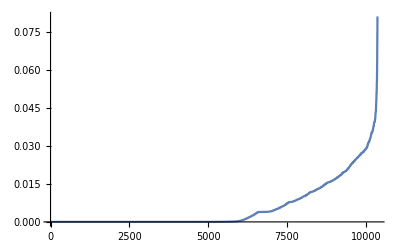

```mathematica
ListLinePlot[Sort[Flatten[depthsiter[[1;;-1;;10,1;;-1;;10]]]],PlotRange->All]
```

#### Plot depth with a normalized scale

```mathematica
Image[#/Max[Flatten[#]]&[depthsiter]]
```

-Graphics-

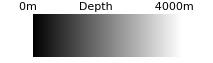

```mathematica
Show[Graphics[{Style[Text["0m            Depth            4000m",{100,60}],14]}],Image[Table[i,{j,0,1,0.02},{i,0,1,0.005}]]]
```

#### Run each stepper to access cached data, obtain flow information, reconstruct flow direction, plot it.

```mathematica
NewDepthDelta1Dperiodic[dat,depthsiter,0.5];
ewflow=eamat(adjustedlosses[[All,2;;-2,2]]-adjustedlosses[[All,2;;-2,1]]);
NewDepthDelta1Daperiodic[dat,depthsiter,0.5];
nsflow=eamat Transpose[adjustedlosses[[All,2;;-2,1]]-adjustedlosses[[All,2;;-2,2]]];
angflow=(ArcTan[nsflow/(0.00000001+ewflow)]+π (0.5-0.5Sign[ewflow])+2π(0.5+0.5Sign[ewflow])(0.5-0.5Sign[nsflow]))/(2π);
flowim=Image[Transpose[{angflow,1+0angflow,(#/Max[Flatten[#]])^0.25&[Sqrt[nsflow^2+ewflow^2]]},{3,1,2}],ColorSpace->"HSB"]
```

-Graphics-

```mathematica
Show[Graphics[{Style[Text["Flow direction",{100,210}],14]}],Image[Table[If[i>0&&Abs[j]<0.1,{0,0,1},{(ArcTan[j/(0 0.00000001+i)]+π (0.5-0.5Sign[i])+2π(0.5+0.5Sign[i])(0.5-0.5Sign[j]))/(2π),If[Sqrt[i^2+j^2]<1,1,0],Sqrt[i^2+j^2]}],{j,1-0.005,-1,-0.01},{i,-1+0.005,1,0.01}],ColorSpace->"HSB"],Graphics[Style[Text["Relative flux",{150,100}],14]]]
```

-Graphics-

#### Examine areas of high erosion by overplotting flux and gradient

```mathematica
totalflow=Sqrt[ewflow^2+nsflow^2];
absgrad=#/Max[Flatten[#]]&[(Sqrt[((dat+0depthsiter)[[2;;-1,1;;-2]]-(dat+0depthsiter)[[1;;-2,1;;-2]])^2+((dat+0depthsiter)[[1;;-2,2;;-1]]-(dat+0depthsiter)[[1;;-2,1;;-2]])^2])];
rivers=Image[(#/Max[Flatten[#]])^0.25&[totalflow]];
gradim=Image[Transpose[{0.5-0.55absgrad^0.125,1+0absgrad,ImageData[rivers][[1;;-2,1;;-2]]},{3,1,2}],ColorSpace->"HSB"]
```

-Graphics-

```mathematica
Show[Graphics[{Style[Text["Relative\n topographic\n gradient",{280,100}],14],Style[Text["Relative\n flux",{100,-50}],14]}],Image[Table[{i,1,j},{i,1,0.5,-0.0025},{j,0,1,0.005}],ColorSpace->"HSB"]]
```

-Graphics-

#### Have a close look at southeast Argyre

```mathematica
Image[Riffle[#,#]&[ImageData[gradim][[-150;;-95,510;;705]]],ColorSpace->"HSB"]
```

-Graphics-

#### A more traditional depiction of land, rivers, ocean.

```mathematica
rivdat=ImageData[rivers];
oceans=dat[[1;;-2,1;;-2]];
wet=(0.5+0.5Sign[0.0000000001dat+depthsiter-0.0002])[[1;;-2,1;;-2]](0.5-0.5Sign[#/Max[Flatten[#]]-0.005])&[Sqrt[(#[[2;;-1,1;;-2]]-#[[1;;-2,1;;-2]])^2+(#[[1;;-2,1;;-2]]-#[[1;;-2,2;;-1]])^2]]&[dat+depthsiter];
depthoceans=depthsiter[[1;;-2,1;;-2]]/Max[Flatten[depthsiter]];
colorwater=Transpose[{(1-wet)oceans,(1-wet)rivdat[[1;;-2,1;;-2]]^0.5,wet(1-depthoceans^4)},{3,1,2}];
im=Image[colorwater]
```

-Graphics-

#### Plotting the whole thing on a sphere for fun - flow directions have been modified so up is still up, rather than north, which is not well defined at the pole

```mathematica
NewDepthDelta1Dperiodic[dat,depthsiter,0.5];
ewflow=eamat(adjustedlosses[[All,2;;-2,2]]-adjustedlosses[[All,2;;-2,1]]);
NewDepthDelta1Daperiodic[dat,depthsiter,0.5];
nsflow=eamat Transpose[adjustedlosses[[All,2;;-2,1]]-adjustedlosses[[All,2;;-2,2]]];
angflow=(ArcTan[nsflow/(0.00000001+ewflow)]+π (0.5-0.5Sign[ewflow])+2π(0.5+0.5Sign[ewflow])(0.5-0.5Sign[nsflow]))/(2π);
angflow+=Table[-i,{720},{i,0.,1,1/1439}];
angflow=Mod[angflow,1];
flowimfix=Image[Transpose[{angflow,1+0angflow,(#/Max[Flatten[#]])^0.25&[Sqrt[nsflow^2+ewflow^2]]},{3,1,2}],ColorSpace->"HSB"];
```

```mathematica
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2π},PlotStyle->Texture[flowimfix],TextureCoordinateFunction->({#5, -#4}&),Boxed->False,Axes->None,Mesh->None,Lighting->"Neutral",ImageSize->600,PlotPoints->70,ViewPoint->{0,0,-5},ViewAngle->0.2]
```

-Graphics3D-

```mathematica
Show[Graphics[{Style[Text["Flow direction",{100,210}],14]}],Image[Table[If[i>0&&Abs[j]<0.1,{0,0,1},{(ArcTan[j/(0 0.00000001+i)]+π (0.5-0.5Sign[i])+2π(0.5+0.5Sign[i])(0.5-0.5Sign[j]))/(2π),If[Sqrt[i^2+j^2]<1,1,0],Sqrt[i^2+j^2]}],{j,1-0.005,-1,-0.01},{i,-1+0.005,1,0.01}],ColorSpace->"HSB"],Graphics[Style[Text["Relative flux",{150,100}],14]]]
```

-Graphics-